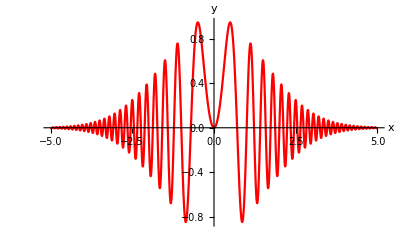

```mathematica
(* Příklad 1 *)
ClearAll["Global`*"]
f[ω_,θ_,t_] := Sin[ω*t] ⅇ^(-t^2/(2*θ^2))
Plot[{f[2*π*x,1.5,x]},{x,-5,5},PlotRange->All, AxesLabel-> {"x","y"}, PlotStyle->Red]
```

```mathematica
(* Příklad 2 *)
ClearAll["Global`*"]
uloha={-Subscript[x, 2]+3 Subscript[x, 1]==3,-6 Subscript[x, 1]+17 Subscript[x, 2]+2 Subscript[x, 3]==14,-21 Subscript[x, 1]+15 Subscript[x, 3]==3};
vyr=Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3];

reseni=Solve[uloha];
vyr/.reseni
```

{75/239}

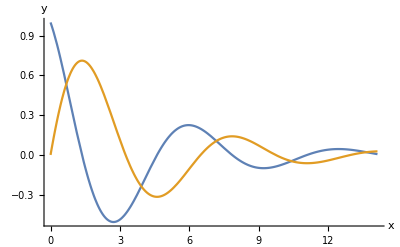

```mathematica
(* Příklad 3 *)
ClearAll["Global`*"]
soustavaRovnic={x1'[t]==-x2[t]-0.5*x1[t],x2'[t]==x1[t]};
soustavaPodminek={x1[0]==1,x2[0]==0};

tmax=(9*π)/2;
sjednoceno=Union[soustavaRovnic,soustavaPodminek];
dif={x1[t],x2[t]};
vysledek=NDSolve[sjednoceno,dif,{t,0,tmax}];
Plot[Evaluate[dif/.vysledek],{t,0,tmax}, PlotRange->All, AxesLabel->{"x","y"}]
```